```mathematica
Get[NotebookDirectory[]<>"25_02_18_combine_packages_1.wls"];
(*equations[pars[-8]]*)
```

```mathematica
w/.pars[0]
```

28

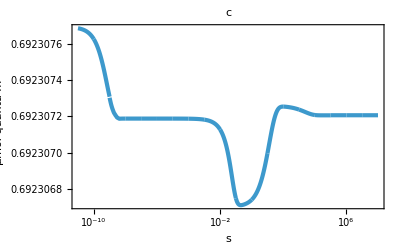
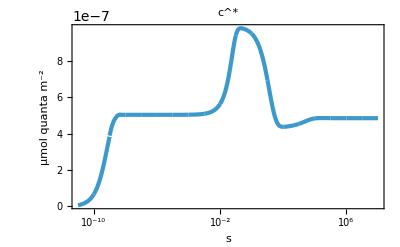
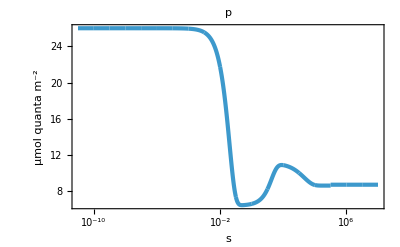
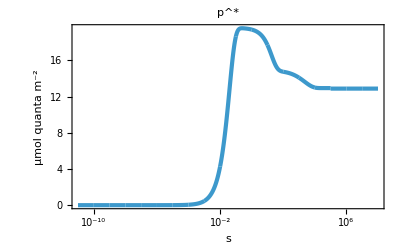
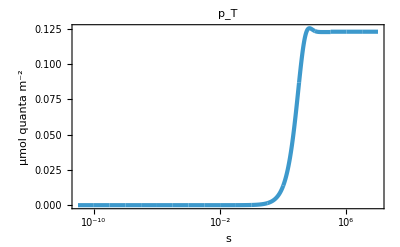
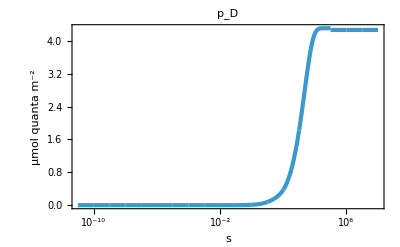
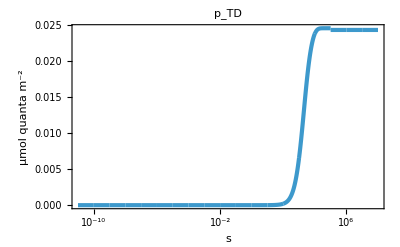
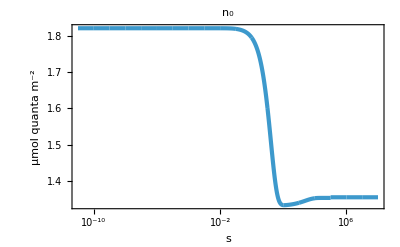

```mathematica
(Export[NotebookDirectory[]<>"export/simulation-all-scales.pdf",#];#)&@(*Framed[*)GridMap[plotSimulationStitch[#,Table[{Join[{L->800,tmin->0,tmax-> "tmax"/.timeRange[i]},pars[i]],{"tmin"/.timeRange[i],"tmax"/.timeRange[i]}},{i,-10,8,1}],{imageSizePadding[ImagePaddingExtra3],FrameLabel->{{#/.units,None},{"s",None}},PlotLabel->(#/.names)}]&,quants](*,RoundingRadius->gridRounding]*)
```

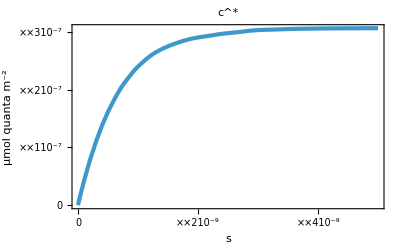
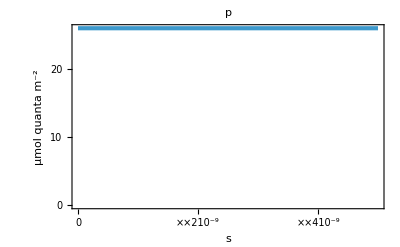
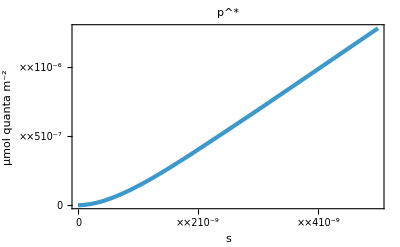

```mathematica
(Export[NotebookDirectory[]<>"export/photochem-scale-1.pdf",#];#)&@Framed[GridMap[plotSimulation[#,Join[{L->500,tmin->0,tmax-> 5 10^-9},pars[-8]],{0,5 10^-9},{AxesOrigin->{0,0},PlotLabel->(#/.names),FrameLabel->{{#/.units,None},{"s",None}},ImagePadding->ImagePaddingExtra}]&,{{cX},{p,pX}}],RoundingRadius->gridRounding]
```

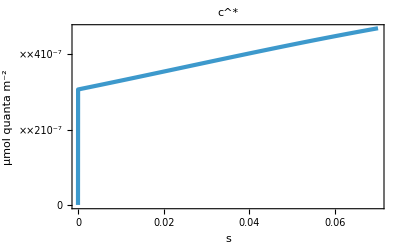
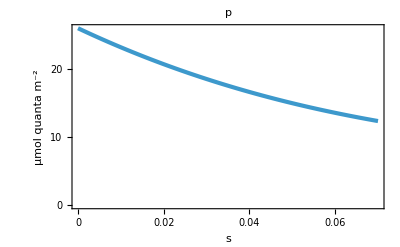
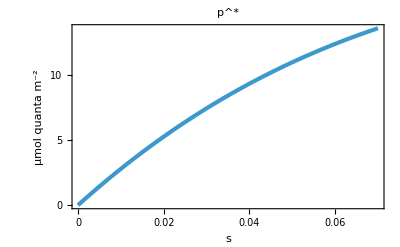

```mathematica
(Export[NotebookDirectory[]<>"export/photochem-scale-2.pdf",#];#)&@Framed[GridMap[plotSimulation[#,Join[{L->500,tmin->0,tmax-> .07},pars[0]],{0,.07},{AxesOrigin->{0,0},PlotLabel->(#/.names),FrameLabel->{{#/.units,None},{"s",None}},ImagePadding->ImagePaddingExtra}]&,{{cX},{p,pX}(*,{n0,n,nX}*)}],RoundingRadius->gridRounding]
```

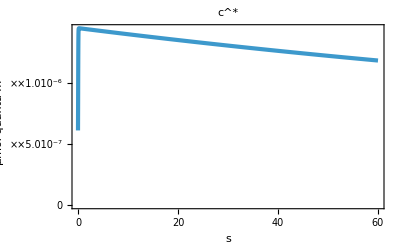
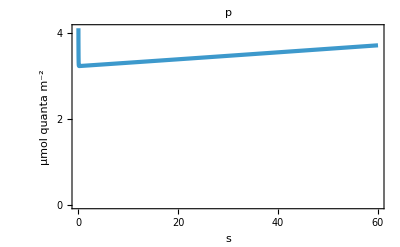
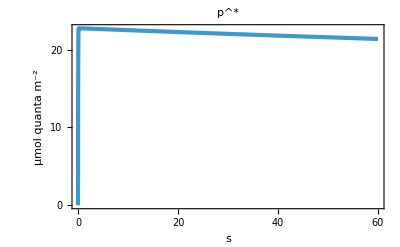
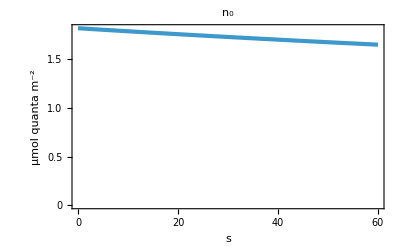
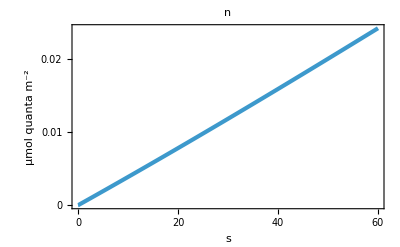
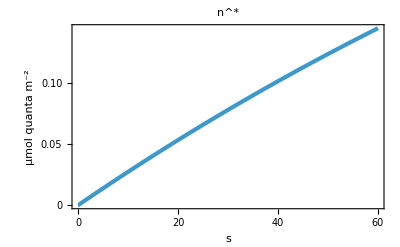

```mathematica
(Export[NotebookDirectory[]<>"export/photochem-scale-3.pdf",#];#)&@Framed[GridMap[plotSimulation[#,Join[{L->1000,tmin->0,tmax-> 60},pars[-4]],{0,60},{AxesOrigin->{0,0},PlotLabel->(#/.names),FrameLabel->{{#/.units,None},{"s",None}},ImagePadding->ImagePaddingExtra}]&,{{cX},{p,pX},{n0,n,nX}(*,{gP,gN,gU},{hP,FvFm,ϕPSII}*)}],RoundingRadius->gridRounding]
```

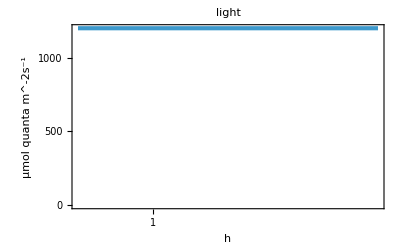
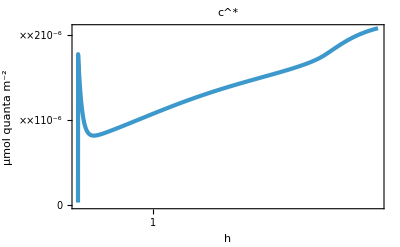
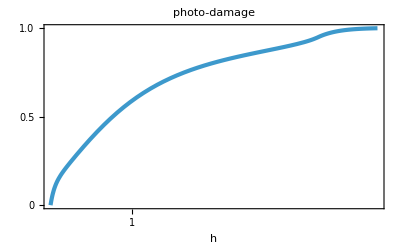
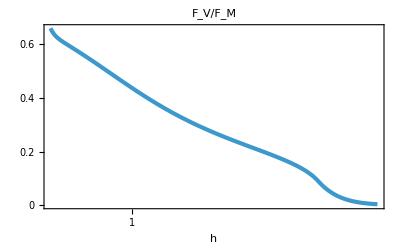

```mathematica
(Export[NotebookDirectory[]<>"export/photochem-scale-4.pdf",#];#)&@Framed[GridMap[plotSimulation[#,Join[{L->1200,tmin->0,tmax-> 4 3600},pars[4]],{0,4 3600},{AxesOrigin->{0,0},PlotLabel->(#/.names),FrameLabel->{{#/.units,None},{"h",None}},PlotRange->Full,ImagePadding->ImagePaddingExtra,{FrameTicks->{{autoTicks,None},{hourTicks,None}}}}]&,{{L},{ cX},{damage,FvFm}}],RoundingRadius->gridRounding]
```